```mathematica
phi[x_,q_,m_]:=(2 q)/(√(q^2-m^2)) ArcTan[x/(√(q^2-m^2))]
h[x_,q_,m_]:=ⅇ^(-m/q phi[x,q,m])
R2[x_,q_,m_]:=(x^2+(q^2-m^2))/h[x,q,m]
hup[u_,a_,q_,m_]:=If[u≠0,h[1/u-a,q,m],ⅇ^(-m π √(1/(-m^2+q^2)))]
hum[u_,a_,q_,m_]:=If[u≠0,h[1/u-a,q,m],ⅇ^(m π √(1/(-m^2+q^2)))]
uR2up[u_,a_,q_,m_]:=(1-2 a u+(a^2-m^2+q^2) u^2)/hup[u,a,q,m]
uR2um[u_,a_,q_,m_]:=(1-2 a u+(a^2-m^2+q^2) u^2)/hum[u,a,q,m]
Gall[u_,a_,b_,q_,m_,lor_]:=If[lor==1,uR2up[u,a,q,m](uR2up[u,a,q,m] 1/b^2-hup[u,a,q,m] u^2),uR2um[u,a,q,m](uR2um[u,a,q,m] 1/b^2-hum[u,a,q,m] u^2)];
```

```mathematica
bc=ⅇ^(-(2 mv ArcTan[(2 mv)/(√(-mv^2+qv^2))])/(√(-mv^2+qv^2))) √(3 mv^2+qv^2);
```

```mathematica
br=ⅇ^(-(2 mv ArcTan[mv/(√(-mv^2+qv^2))])/(√(-mv^2+qv^2))) qv ;
bi=√2 ⅇ^((2 m ArcTan[(-3 m-√(4 m^2+q^2))/(√(-m^2+q^2))])/(√(-m^2+q^2))) √(6 m^2+q^2+3 m √(4 m^2+q^2));
```

```mathematica
Get["C:\\Users\\96031\\Desktop\\Light Ring wrom\\subfunctions.wl"]
```

```mathematica
mv=1.;qv=4.441075597777203;bv=√25;av=3mv;
```

```mathematica
zembedEuc[qv,mv];
zembed[x_]:=zres[x]/.sol
lowerbound=-27 mv;
Bronnikovembed=RevolutionPlot3D[{{Rareal[r,qv,mv],zembed[r]/.sol}},{r,lowerbound,changesign},AspectRatio->1,Mesh->None,Axes->None,Boxed->False,PlotStyle->GrayLevel[.8],ColorFunction->Hue,Lighting->"Neutral"];
radia=√R2[#,qv,mv]&;
impact=3.9023234704840597;
```

```mathematica
throatlocat=ParametricPlot3D[{radia[-mv ] Cos[x],radia[-mv ]Sin[x],zembed[-mv]},{x,0,2 π},PlotStyle->{White,Thickness[0.00002]}];
lringlocat=ParametricPlot3D[{radia[-2 mv ] Cos[x],radia[-2 mv ]Sin[x],zembed[-2 mv]},{x,0,2 π},PlotStyle->{Pink,Thickness[0.0002]}];
upbound=ParametricPlot3D[{radia[changesign ] Cos[x],radia[changesign ]Sin[x],zembed[changesign]},{x,0,2 π},PlotStyle->{RGBColor[0,0.6,.3],Thickness[0.0002]}];
lowbound=ParametricPlot3D[{radia[lowerbound ] Cos[x],radia[lowerbound ]Sin[x],zembed[lowerbound]},{x,0,2 π},PlotStyle->{RGBColor[0,0.6,.3],Thickness[0.0002]}];
```

```mathematica
plussmallb=plot3d[2.2,qv,mv,radia,{RGBColor[1,.5,.3],Thickness[0.002]},1];
plussmallbalt=plot3dalt[2.2,qv,mv,radia,{RGBColor[1,.5,.3],Thickness[0.002]},1];
plus1loop=plot3d[impact,qv,mv,radia,{RGBColor[1,0.1,0],Thickness[0.002]},1];
plus1loopalt=plot3dalt[impact,qv,mv,radia,{RGBColor[1,0.1,0],Thickness[0.002]},1];
pluslargeb=plot3d[5.2,qv,mv,radia,{RGBColor[.8,.4,.1],Thickness[0.002]},1];
minussmallb=plot3d[1.2,qv,mv,radia,{RGBColor[.5,.1,0],Thickness[0.002]},-1];
minusmedb=plot3d[impact,qv,mv,radia,{RGBColor[.1,.1,1],Thickness[0.002]},-1];
minuslargeb=plot3d[6.2,qv,mv,radia,{RGBColor[.7,.2,0.7],Thickness[0.002]},-1];
Show[Bronnikovembed,throatlocat,lringlocat,plussmallb,plussmallbalt,plus1loop,plus1loopalt,pluslargeb,minusmedb,minuslargeb]
```

InterpolatingFunction::dmval: 输入值 {0.785398} 位于插值函数的数据范围之外. 将使用外推法.

Power::infy: 碰到无穷表达式 1/0.

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

-Graphics3D-

```mathematica
V[r_]=(h[r,q,m]/R2[r,q,m]-ϵ h[r,q,m]/L^2);ϵ=-1;
risco=-3 m-√(4 m^2+q^2);
Lisco=Re[(ⅇ^((m ArcTan[r/(√(-m^2+q^2))])/(√(-m^2+q^2))) √m √(m^2-q^2-r^2))/(√(2 m+r))/.r->risco];
Lisco/.{m->mv,q->qv}//N
```

2.89606

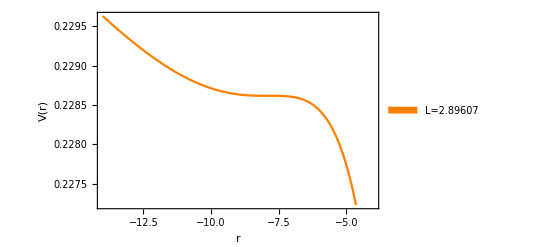

```mathematica
Plot[{V[r]/.L->Lisco/.{m->mv,q->qv}},{r,-14,-4},FrameLabel->{"r","V(r)"},Frame->True,PlotLegends->Placed[SwatchLegend[Style[TraditionalForm[#],15]&/@{"L=2.89607","L=1.485","Q=2.19556"}],{0.8,0.85}],PlotStyle->Orange]
```

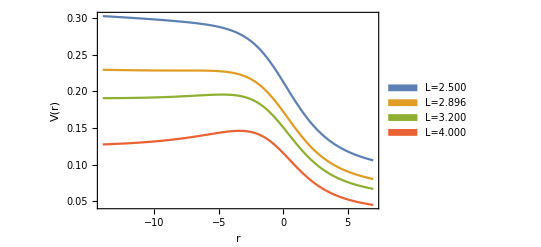

```mathematica
Plot[{V[r]/.L->2.5/.{m->mv,q->qv},V[r]/.L->Lisco/.{m->mv,q->qv},V[r]/.L->3.2/.{m->mv,q->qv},V[r]/.L->4/.{m->mv,q->qv}},{r,-14,7},FrameLabel->{"r","V(r)"},Frame->True,PlotLegends->Placed[SwatchLegend[Style[TraditionalForm[#],15]&/@{"L=2.500","L=2.896","L=3.200","L=4.000"}],{0.83,0.77}]]
```

```mathematica
totalphi4I[b_,q_,m_,lor_]/;1/b^2<h[-2m,q,m]/R2[-2m,q,m]:=2totalphi[b,q,m,lor]
totalphi4I[b_,q_,m_,lor_]/;1/b^2≥ h[-2m,q,m]/R2[-2m,q,m]:=totalphi[b,q,m,lor]-totalphi[b,q,m,-lor]
rofm[b_,q_,m_,1]/;1/b^2<h[-2m,q,m]/R2[-2m,q,m]:=Block[{av,tphi,sol,u,tphim,um,rm},
av=3m;
tphi=totalphi[b,q,m,1];
sol=NDSolve[{D[u[x],x]== Re@√Gall[u[x],av,b,q,m,1],u[0]==0},u,{x,0,tphi}];
tphim=(2tphi/Pi-0.5)//Floor;
tphim=Range[0,tphim];
tphim=0.5 Pi+Pi tphim;
um=If[#<=tphi,u[#],u[2tphi-#]]&/@tphim/.sol[[1]];
rm=1/um-av
]
rofm[b_,q_,m_,-1]/;1/b^2<h[-2m,q,m]/R2[-2m,q,m]:=Block[{av,tphi,sol,u,tphim,um,rm},
av=0;
tphi=totalphi[b,q,m,-1];
sol=NDSolve[{D[u[x],x]== Re@√Gall[u[x],av,b,q,m,-1],u[0]==0},u,{x,0,tphi}];
tphim=-(2tphi/Pi+0.5)//Floor;
tphim=Range[0,tphim];
tphim=-0.5 Pi-Pi tphim;
um=If[#>=tphi,u[#],u[2tphi-#]]&/@tphim/.sol[[1]];
rm=1/um-av
]
rofm[b_,q_,m_,1]/;1/b^2≥ h[-2m,q,m]/R2[-2m,q,m]:=Block[{av,r0,u0,tphi,sol,avp,u,x,tphip,solp,tphim,um,rm},
tphi=totalphi[b,q,m,1];
tphip=totalphi[b,q,m,-1];
tphip=tphi-tphip;
tphim=(tphip/Pi-0.5)//Floor;
tphim=Range[0,tphim];
If[tphim==={},Return[{}]];
av=3m;
sol=NDSolve[{D[u[x],x]==Re@√Gall[u[x],av,b,q,m,1],u[0]==0},u,{x,0,tphi}];
avp=0;
r0=-m;
u0=1/(r0+avp);
solp=NDSolve[{D[u[x],x]==Re@√Gall[u[x],avp,b,q,m,-1],u[tphi]==u0},u,{x,tphi,tphip}];
tphim=0.5 Pi+Pi tphim;
um=If[#<=tphi,{u[#]/.sol[[1]],1},{u[#]/.solp[[1]],-1}]&/@tphim;
rm=If[#[[2]]>0,1/#[[1]]-av,1/#[[1]]-avp]&/@um
]
```

```mathematica
rofm[b_,q_,m_,-1]/;1/b^2≥ h[-2m,q,m]/R2[-2m,q,m]:=Block[{av,r0,u0,tphi,sol,avp,u,x,tphip,solp,tphim,um,rm},
tphi=totalphi[b,q,m,-1];
tphip=totalphi[b,q,m,1];
tphip=tphi-tphip;
tphim=-(tphip/Pi+0.5)//Floor;
tphim=Range[0,tphim];
If[tphim==={},Return[{}]];
av=0;
sol=NDSolve[{D[u[x],x]==Re@√Gall[u[x],av,b,q,m,-1],u[0]==0},u,{x,0,tphi}];
avp=3m;
r0=-m;
u0=1/(r0+avp);
solp=NDSolve[{D[u[x],x]==Re@√Gall[u[x],avp,b,q,m,1],u[tphi]==u0},u,{x,tphi,tphip}];
tphim=-0.5 Pi-Pi tphim;
um=If[#≥ tphi,{u[#]/.sol[[1]],1},{u[#]/.solp[[1]],-1}]&/@tphim;
rm=If[#[[2]]>0,1/#[[1]]-av,1/#[[1]]-avp]&/@um
]
```

```mathematica
Iob[Iem_,b_,q_,m_,lor_]:=Block[{rofmv},
rofmv=rofm[b,q,m,lor];
If[lor==1,
h[#,q,m]^2/(ⅇ^(-(m π)/(√(-m^2+q^2)))) Iem[#]&/@rofmv//Total,h[#,q,m]^2/(ⅇ^((m π)/(√(-m^2+q^2)))) Iem[#]&/@rofmv//Total]
]
```

```mathematica
Iem1[r_]:=Piecewise[{{0,r<=risco},{(1/(r-(risco-1)))^2,r>risco}},0];
Plot[Iem1[r],{r,-6,12},PlotRange->{{-6,12},{0,1}},AxesLabel->{r,"\!\(\*SubscriptBox[\(I\), \(em1\)]\)(r)"}]
```

-Graphics-

```mathematica
Plot[Iem1[r],{r,-6,12},PlotRange->All,PlotRange->{{-6,12},{0,1}},AxesLabel->{r,"\!\(\*SubscriptBox[\(I\), \(em1\)]\)(r)"}]
```

-Graphics-

```mathematica
Iem1[r_]:=If[r<=risco,0,1/(r-(risco-1))^2]
Plot[Iem1[r],{r,-1,10},PlotRange->Automatic,Frame->True,FrameLabel->{"r","I_em1"},LabelStyle->{16}]
```

-Graphics-

```mathematica
Iem2[r_]:=If[(-ArcTan[r-5]+π/2)/(-ArcTan[-4]+π/2),r>1]
Plot[Iem1[r],{r,0,8},PlotRange->Automatic,Frame->True,FrameLabel->{"r","I_em2"},LabelStyle->{10}]
```

-Graphics-